# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

H:\My Drive\Doctorado\Quinto semestre\RESEARCH\Quantum maps\Codes\my test\Initial conditions

```mathematica
Get["QMB.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[qubit];
qubit[θ_,ϕ_]:=FullSimplify[Normalize[{Cos[θ/2],Exp[I ϕ]Sin[θ/2]}]];
Clear[coherentstate];
coherentstate[state_,L_]:=Flatten[KroneckerProduct@@Table[state,L]];
```

```mathematica
ClearAll[Superoperator](*nuevo*)
Superoperator[t_,ψ0E_,eigVals_,eigVecs_,L_]:=
	Module[{ψf,ρfSE(*SE final state*)},
		ψf=StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[#],ψ0E],eigVals,eigVecs]&/@{{0},{1}};
		ρfSE=Dyad[ψf[[#1]],ψf[[#2]]]&@@@Tuples[{1,2},2];
		Transpose[Flatten[MatrixPartialTrace[#,2,{2,2^(L-1)}]]&/@ρfSE]
	]
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Regular

## LDoS caotico

## Hamiltonian

```mathematica
(*Set parameters in integrable region and compute Hamiltonian, and its eigenvalues and eigenvectors*)
L=10(*number of spins*);
{hx,hz,J}={1,0.5,ConstantArray[1,L-1]};
```

{0.534009,0.53672}

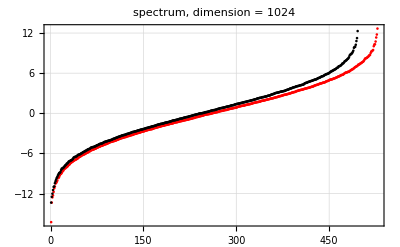

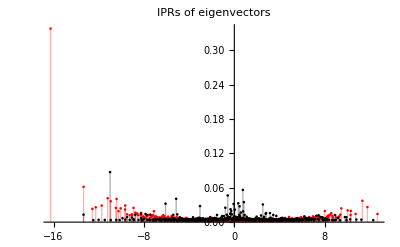

-Graphics-

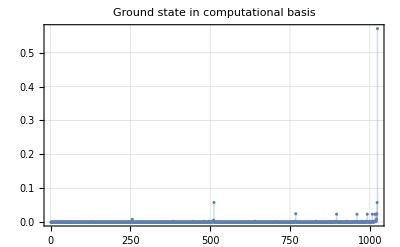

```mathematica
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
OddEigVals=Complement[eigVals,EvenEigVals];
OddEigVecs=Complement[eigVecs,evenEigenVecs];
{MeanLevelSpacingRatio[OddEigVals],MeanLevelSpacingRatio[EvenEigVals]}
ListPlot[{EvenEigVals,OddEigVals},PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Red,Black},ImageSize->400,PlotLabel->Style["spectrum, dimension = "<>ToString[2^L],25,Black]]
iprM=ParallelTable[Total[Quiet[Abs[i]^4]],{i,evenEigenVecs}];
iprm=ParallelTable[Total[Quiet[Abs[i]^4]],{i,OddEigVecs}];
ListPlot[{Transpose[{EvenEigVals,iprM}],Transpose[{OddEigVals,iprm}]},PlotRange->All,Filling->Axis,ImageSize->400,PlotStyle->{Red,Black},PlotLabel->Style["IPRs of eigenvectors",25,Black]]
MatrixPlot[H,PlotRange->All,PlotTheme->"Detailed"]
ListPlot[Abs[eigVecs[[1]]]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->400,PlotLabel->Style["Ground state in computational basis",25,Black]]
```

## Initial state all random

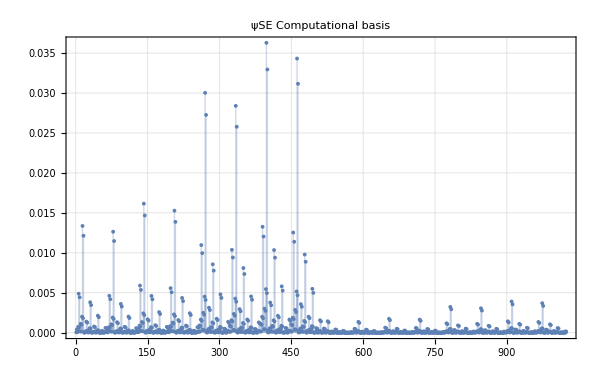
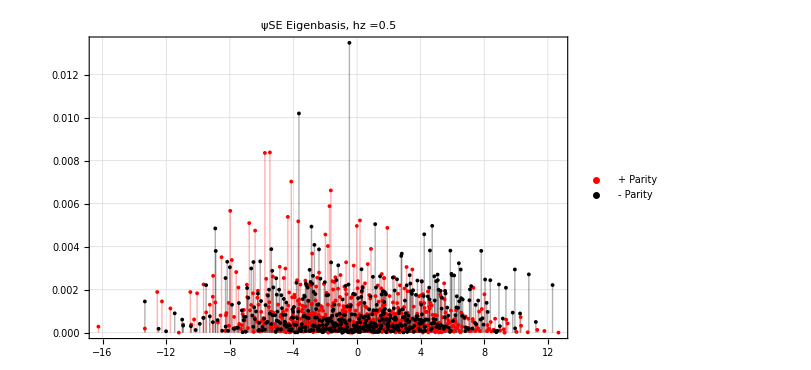

```mathematica
(*Set the seed SeedRandom[32371] and compute three initial states for the environment*)
SeedRandom[32371];
ψ0E=RandomChainProductState[L];
ψ0Espineven=Conjugate[evenEigenVecs].ψ0E;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0E;
plota=ListPlot[Abs[ψ0E]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## Initial state 0random

```mathematica
SeedRandom[32371];
ψ0E=RandomChainProductState[L-1];
ψ0SE=KroneckerVectorProduct[VectorFromKetInComputationalBasis[{0}],ψ0E];
```

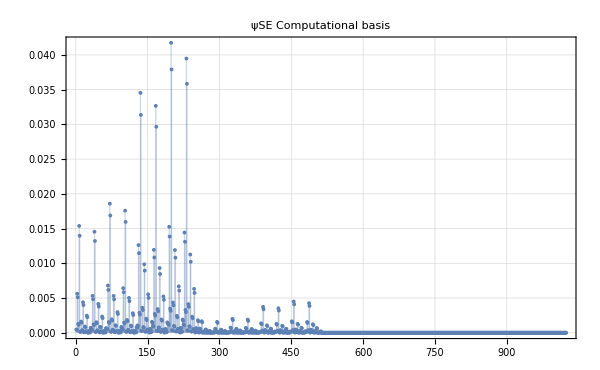
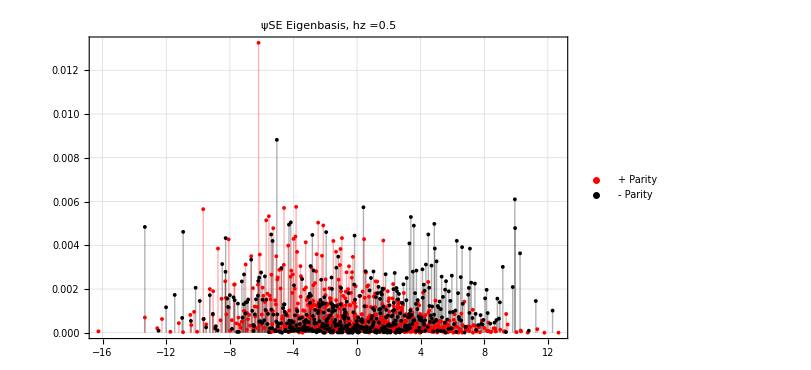

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## Initial state 1random

```mathematica
SeedRandom[32371];
ψ0E=RandomChainProductState[L-1];
ψ0SE=KroneckerVectorProduct[VectorFromKetInComputationalBasis[{1}],ψ0E];
```

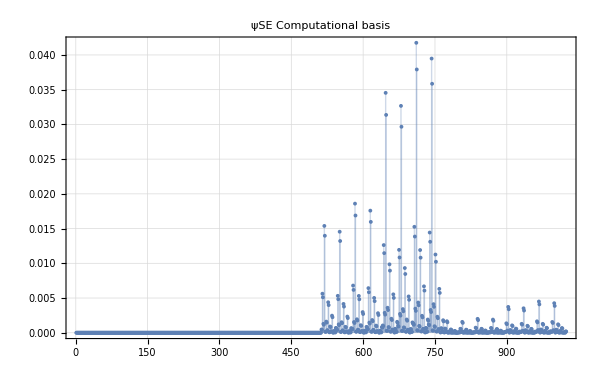
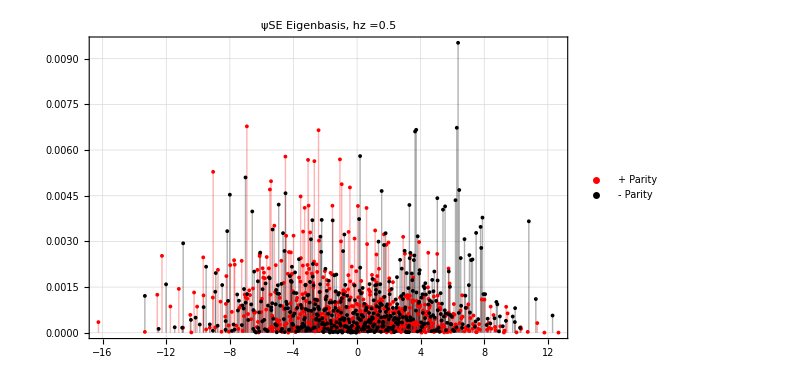

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## Initial state 00..

```mathematica
Clear[ψ0SE];
ψ0SE=VectorFromKetInComputationalBasis[ConstantArray[0,L]];
```

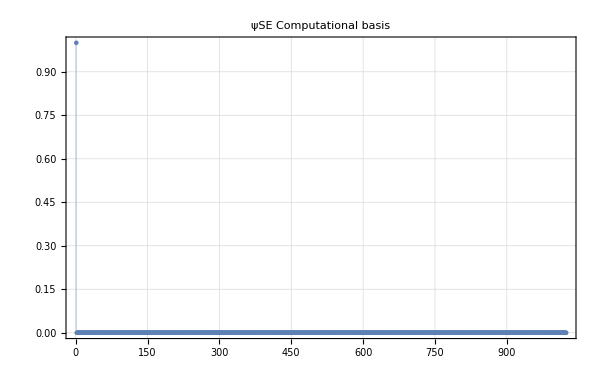
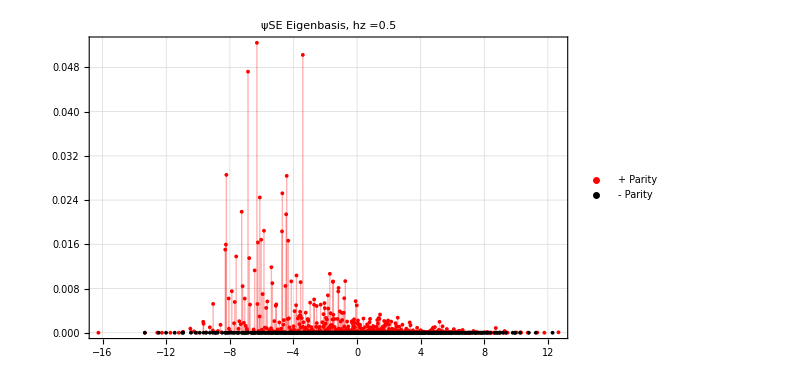

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## Initial state 11..

```mathematica
Clear[ψ0SE];
ψ0SE=VectorFromKetInComputationalBasis[ConstantArray[1,L]];
```

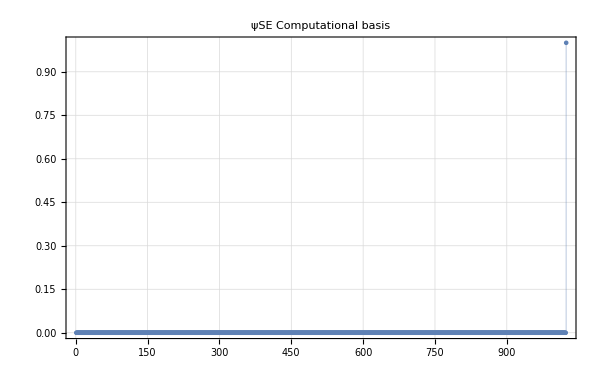
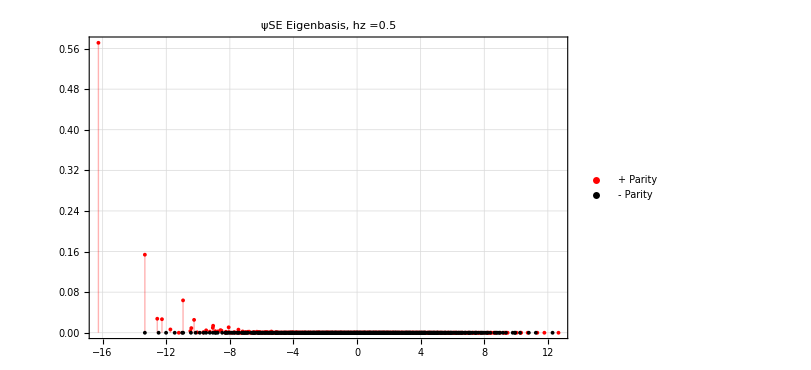

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## Chaotic region (h_z=0.5, J=hx=1), 0<=t<=50

```mathematica
(*SeedRandom[32371];
ψ0SEa=KroneckerVectorProduct[VectorFromKetInComputationalBasis[{0}],ψ0E];
ψ0SEb=KroneckerVectorProduct[VectorFromKetInComputationalBasis[{1}],ψ0E];
ψ0SEc=RandomChainProductState[L];
ψT={ψ0SEa,ψ0SEb,ψ0SEc};*)
```

```mathematica
(*Set the seed SeedRandom[32371] and compute three initial states for the environment*)
ψT=Table[RandomChainProductState[L-1],3];
```

```mathematica
ψT={VectorFromKetInComputationalBasis[ConstantArray[0,L-1]],VectorFromKetInComputationalBasis[ConstantArray[1,L-1]],RandomChainProductState[L-1]};
```

```mathematica
tf=10.;
```

```mathematica
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->400
]
];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]
];,{t,0,tf,.1}];
AppendTo[listplots,
ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","eigenvalues( Choi )"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->500]];
,{i,3}]
```

```mathematica
Export["bloch_sphere_and_choi_eigenvalues_regular.avi",Table[GraphicsGrid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],ImageSize->{1000,1200},Spacings->{50,50},Alignment->{Center,Bottom}],{t,0,tf,0.1}],"ImageResolution"->350,"FrameRate"->4,"VideoCompression"->"MPEG4"];
```

```mathematica
grids=Table[GraphicsGrid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],ImageSize->{1000,1200},Spacings->{50,50},Alignment->{Center,Bottom}],{t,0,tf,0.1}];
```

```mathematica
grids[[1]]
```

```mathematica
Export["chaotic_frame_"<>ToString[#]<>".png",grids[[#]],ImageResolution->200]&/@Range[Length[grids]];
```

```mathematica
Export["regular_frame_"<>ToString[#]<>".png",grids[[#]],ImageResolution->200]&/@Range[Length[grids]];
```

## LDoS regular

## Hamiltonian

```mathematica
(*Set parameters in integrable region and compute Hamiltonian, and its eigenvalues and eigenvectors*)
L=8(*number of spins*);
{hx,hz,J}={1,3.,ConstantArray[1,L-1]};
```

{0.366177,0.340819}

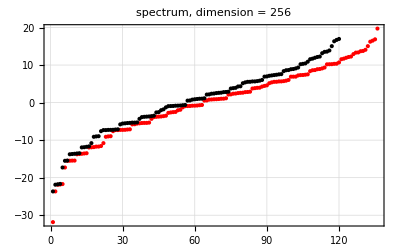

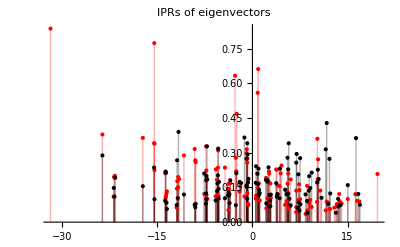

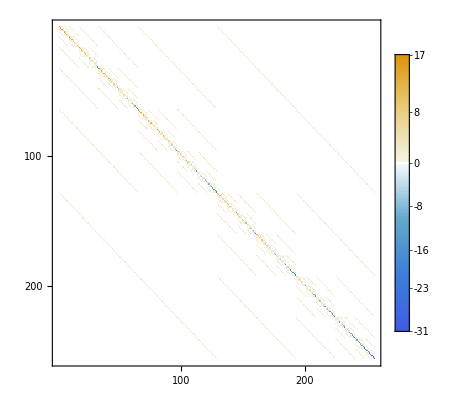

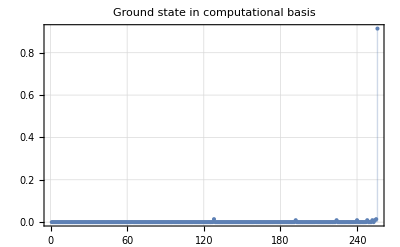

```mathematica
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
OddEigVals=Complement[eigVals,EvenEigVals];
OddEigVecs=Complement[eigVecs,evenEigenVecs];
{MeanLevelSpacingRatio[OddEigVals],MeanLevelSpacingRatio[EvenEigVals]}
ListPlot[{EvenEigVals,OddEigVals},PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Red,Black},ImageSize->400,PlotLabel->Style["spectrum, dimension = "<>ToString[2^L],25,Black]]
iprM=ParallelTable[Total[Quiet[Abs[i]^4]],{i,evenEigenVecs}];
iprm=ParallelTable[Total[Quiet[Abs[i]^4]],{i,OddEigVecs}];
ListPlot[{Transpose[{EvenEigVals,iprM}],Transpose[{OddEigVals,iprm}]},PlotRange->All,Filling->Axis,ImageSize->400,PlotStyle->{Red,Black},PlotLabel->Style["IPRs of eigenvectors",25,Black]]
MatrixPlot[H,PlotRange->All,PlotTheme->"Detailed"]
ListPlot[Abs[eigVecs[[1]]]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->400,PlotLabel->Style["Ground state in computational basis",25,Black]]
```

```mathematica
(*time points*)
numberOftemporalPoints=50;
tValues=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5x/#+i),{i,0,2},{x,#/5,1,-1}]]&[numberOftemporalPoints];
```

```mathematica
state=qubit[Pi/2,0]
ψ0=coherentstate[state,L];
```

{1/(√2),1/(√2)}

```mathematica
ψ0=RandomChainProductState[L];
```

```mathematica
Module[{ψt},sp=Table[ψt=StateEvolution[t,ψ0,eigVals,eigVecs];
{t,SurvivalProbability[ψ0,ψt]},
{t,tValues}];]
```

```mathematica
ipr=Total[Abs[Conjugate[eigVecs].ψ0]^4]
```

0.0227452

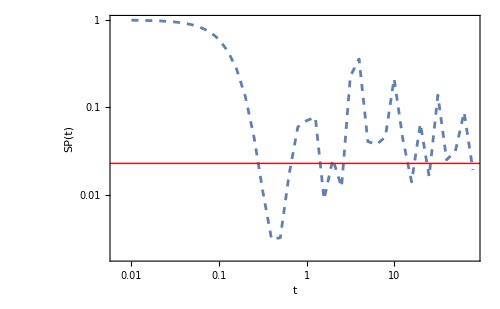

```mathematica
ListLogLogPlot[sp,
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->False,
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]",Rotate["SP(t)",-90Degree]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->500,
Epilog->{Red,InfiniteLine[{1,Log[ipr]},{1,0}]}]
```

## Initial state all random

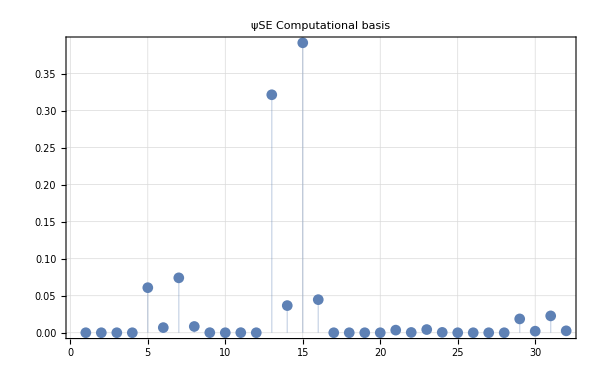
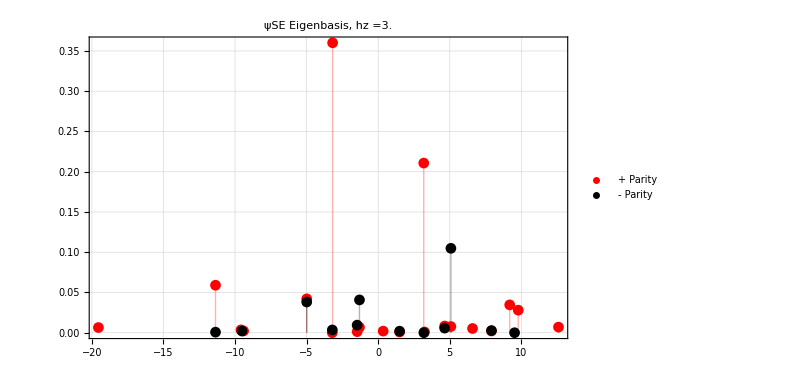

```mathematica
(*Set the seed SeedRandom[32371] and compute three initial states for the environment*)
(*SeedRandom[32371];*)
ψ0E=RandomChainProductState[L];
ψ0Espineven=Conjugate[evenEigenVecs].ψ0E;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0E;
plota=ListPlot[Abs[ψ0E]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## Initial state 0random

```mathematica
(*SeedRandom[32371];*)
ψ0E=RandomChainProductState[L-1];
ψ0SE=KroneckerVectorProduct[VectorFromKetInComputationalBasis[{0}],ψ0E];
```

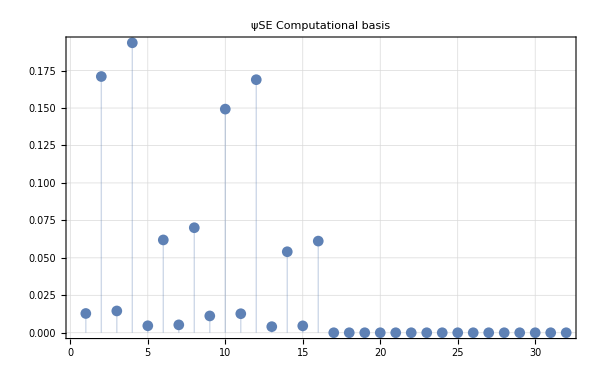
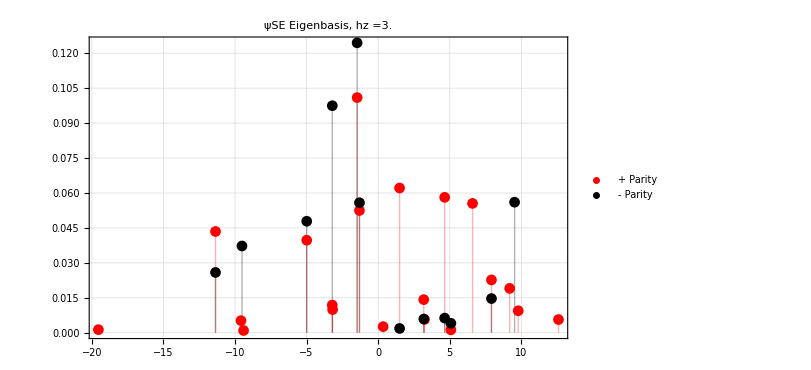

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## Initial state 1random

```mathematica
(*SeedRandom[32371];*)
ψ0E=RandomChainProductState[L-1];
ψ0SE=KroneckerVectorProduct[VectorFromKetInComputationalBasis[{1}],ψ0E];
```

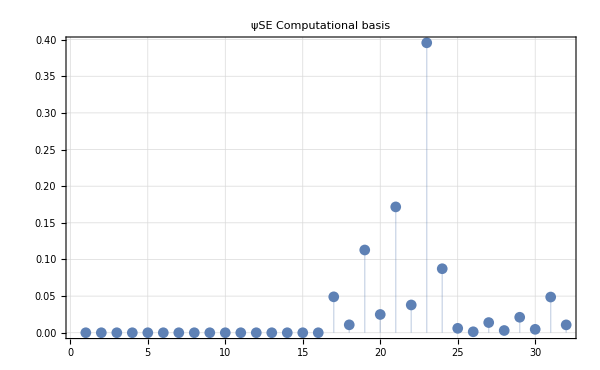
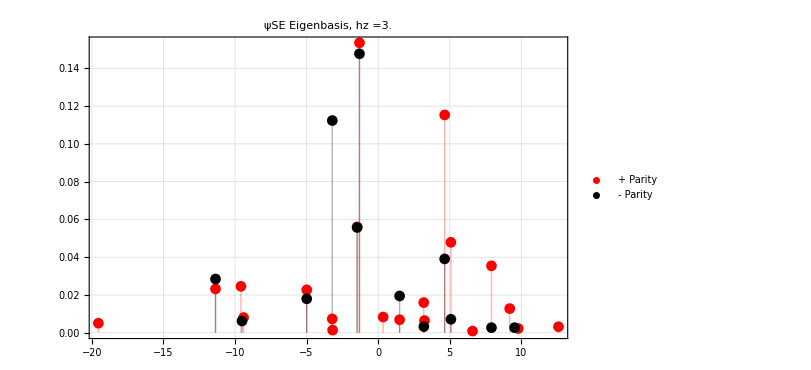

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## Initial state 00..

```mathematica
Clear[ψ0SE];
ψ0SE=VectorFromKetInComputationalBasis[ConstantArray[0,L]];
```

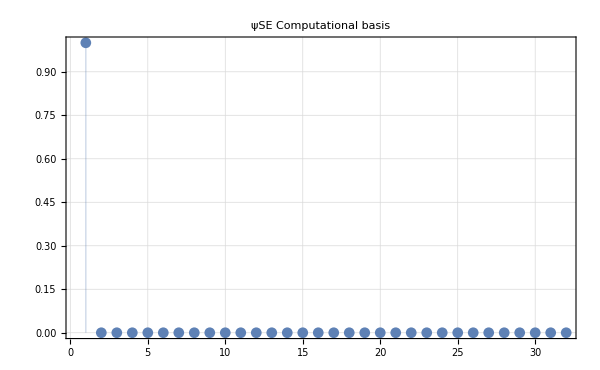
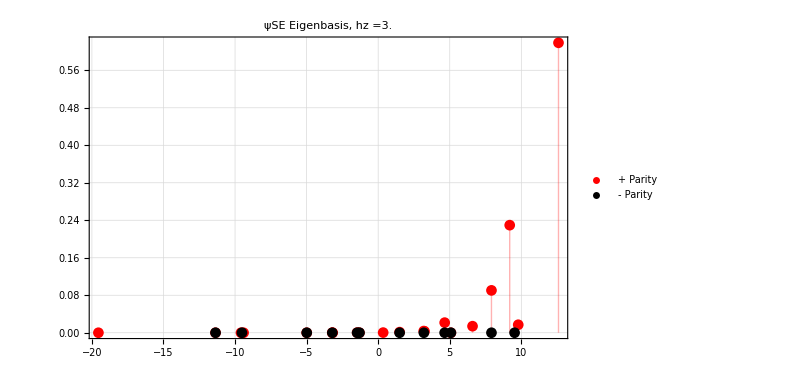

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## Initial state 11..

```mathematica
Clear[ψ0SE];
ψ0SE=VectorFromKetInComputationalBasis[ConstantArray[1,L]];
```

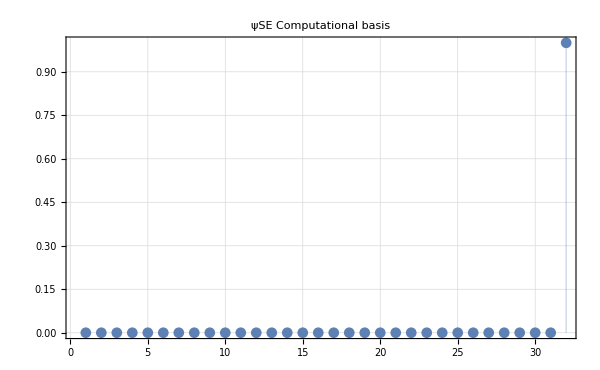
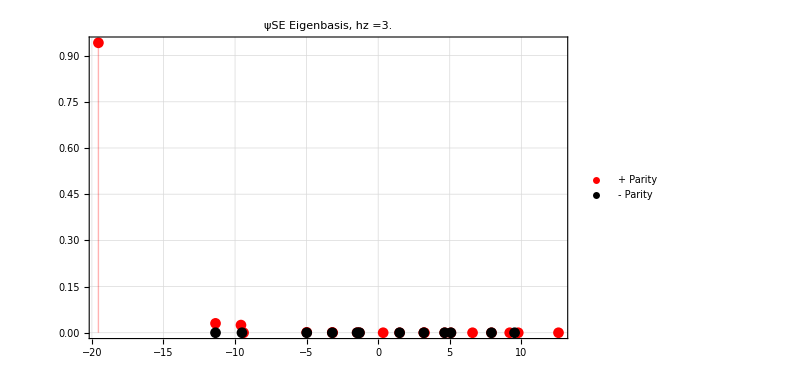

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## Initial state coherent state

```mathematica
Clear[ψ0SE];
state=qubit[Pi/5,-2Pi/5];
ψ0SE=coherentstate[state,L];
```

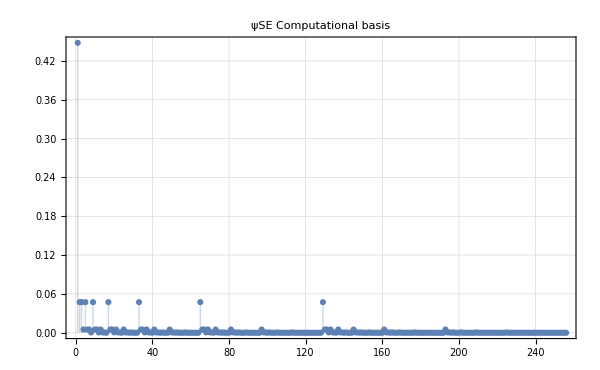
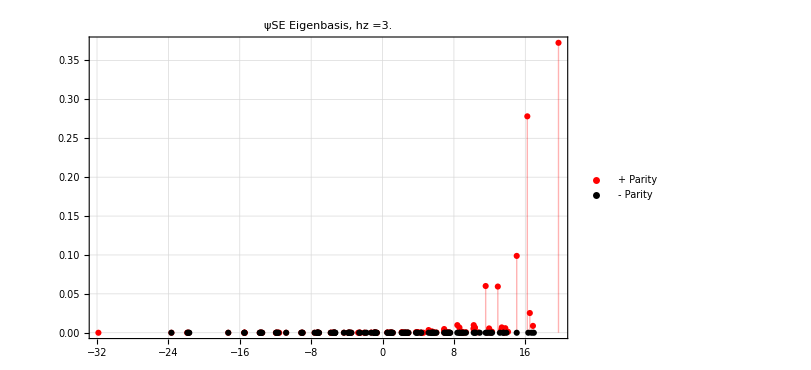

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

```mathematica
Clear[ψ0SE];
state=qubit[Pi/4,Pi/4];
ψ0SE=coherentstate[state,L];
state//MatrixForm
```

(Cos[π/8]
(-1)^(1/4) Sin[π/8])

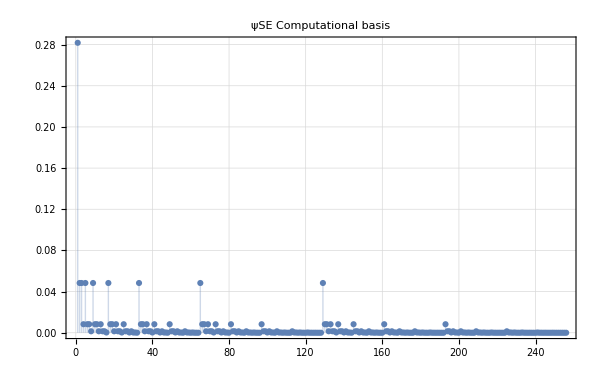
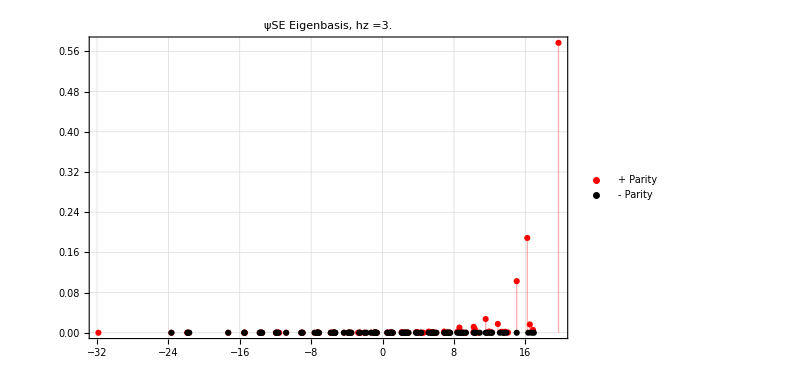

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## Regular (h_z=3.0, J=hx=1), 0<=t<=50

## Choi

```mathematica
(*SeedRandom[32371];
ψ0SEa=KroneckerVectorProduct[VectorFromKetInComputationalBasis[{0}],ψ0E];
ψ0SEb=KroneckerVectorProduct[VectorFromKetInComputationalBasis[{1}],ψ0E];
ψ0SEc=RandomChainProductState[L];
ψT={ψ0SEa,ψ0SEb,ψ0SEc};*)
```

```mathematica
state=qubit[Pi/2,0]
```

{1/(√2),1/(√2)}

```mathematica
(*Set the seed SeedRandom[32371] and compute three initial states for the environment*)
ψT=Table[RandomChainProductState[L-1],3];
```

```mathematica
ψT={VectorFromKetInComputationalBasis[ConstantArray[0,L-1]],VectorFromKetInComputationalBasis[ConstantArray[1,L-1]],RandomChainProductState[L-1]};
```

```mathematica
ψT={coherentstate[state,L-1],VectorFromKetInComputationalBasis[ConstantArray[1,L-1]],RandomChainProductState[L-1]};
```

```mathematica
tf=2.;
```

```mathematica
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->400
]
];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]
];,{t,0,tf,0.1}];
AppendTo[listplots,
ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","eigenvalues( Choi )"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->500]];
,{i,3}]
```

```mathematica
Export["bloch_sphere_and_choi_eigenvalues_regular.avi",Table[GraphicsGrid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],ImageSize->{1000,1200},Spacings->{50,50},Alignment->{Center,Bottom}],{t,0,tf,0.1}],"ImageResolution"->350,"FrameRate"->4,"VideoCompression"->"MPEG4"];
```

```mathematica
grids=Table[GraphicsGrid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],ImageSize->{1000,1200},Spacings->{50,50},Alignment->{Center,Bottom}],{t,0,tf,0.1}];
```

```mathematica
grids[[1]]
```

```mathematica
Export["new_regular_frame_"<>ToString[#]<>".png",grids[[#]],ImageResolution->200]&/@Range[Length[grids]];
```

## Superoperator

```mathematica
tlist=Range[0,1,0.1];
```

```mathematica
ψE=VectorFromKetInComputationalBasis[ConstantArray[0,L-1]];
```

```mathematica
superoperators={};
Do[
superOperator=Superoperator[t,ψE,eigVals,eigVecs,L];
AppendTo[superoperators,superOperator];
,{t,tlist}];
supereigen=Table[Eigenvalues[i],{i,superoperators}];
```

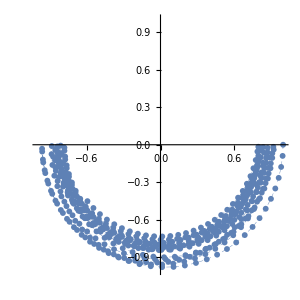
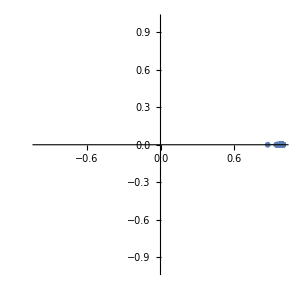
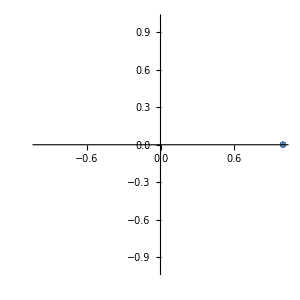
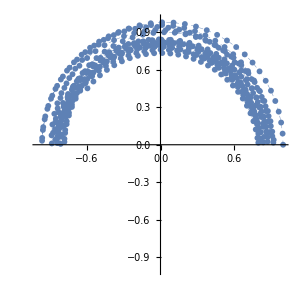

```mathematica
eigenvalsSuperoperator=Chop[Eigenvalues[#]]&/@superoperators;
eigenvalsSorted=SortBy[Transpose[{Re[#],Im[#]}],#[[2]]&]&/@eigenvalsSuperoperator;
ListLinePlot[eigenvalsSorted[[All,#]],PlotRange->{{-1,1},{-1,1}},PlotMarkers->{Automatic,6},PlotStyle->Directive[Dashing[0.01],Thickness[0.001]],ImageSize->300,AspectRatio->1]&/@{1,2,3,4}
```

```mathematica
superoperators={};
Do[
superOperator=Superoperator[t,ψE,eigVals,eigVecs,L];
AppendTo[superoperators,superOperator];
,{t,tlist}];
supereigen=Table[Eigenvectors[i],{i,superoperators}];
```

```mathematica
supereigen//Dimensions
```

{11,4,4}

```mathematica
Table[Norm[supereigen[[i,1]]],{i,Length[superoperators]}]
Table[Norm[supereigen[[i,2]]],{i,Length[superoperators]}]
Table[Norm[supereigen[[i,3]]],{i,Length[superoperators]}]
Table[Norm[supereigen[[i,4]]],{i,Length[superoperators]}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

«1 more identical outputs»